# Lagaris Problem 1: 1st-Order Linear ODE IVP

Solving the ODE in Mathematica:

```mathematica
de=ψ'[x]+(x+(1+3 x^2)/(1+x+x^3))ψ[x] == x^3+2x+x^2(1+3 x^2)/(1+x+x^3)
```

(x+(1+3 x^2)/(1+x+x^3)) ψ[x]+ψ'[x]==2 x+x^3+(x^2 (1+3 x^2))/(1+x+x^3)

```mathematica
generalSolution=FullSimplify[DSolve[de,ψ[x],x]]
```

{{ψ[x]→x^2+(ⅇ^(-x^2/2) C[1])/(1+x+x^3)}}

```mathematica
particularSolution=FullSimplify[DSolve[{de,ψ[0]==1},ψ[x],x]]
```

{{ψ[x]→x^2+(ⅇ^(-x^2/2))/(1+x+x^3)}}

```mathematica
ψa[x_]:=ψ[x]/.particularSolution[[1]]
```

Compute the derivative of the solution.

```mathematica
FullSimplify[D[ψa[x],x]]
```

2 x-(ⅇ^(-x^2/2) (1+x+4 x^2+x^4))/((1+x+x^3)^2)

```mathematica
dψadx[x_]:=2 x-(ⅇ^(-x^2/2) (1+x+4 x^2+x^4))/((1+x+x^3)^2)
```

Plot the analytical solution and its derivatives.

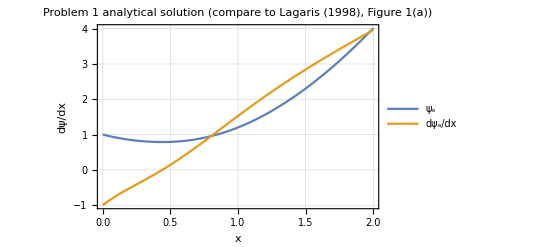

```mathematica
Plot[{ψa[x],dψadx[x]},{x,0,2},AxesLabel->{"x","dψ/dx"},PlotLegends->{"ψ_a","dψ_a/dx"},PlotLabel->"Problem 1 analytical solution (compare to Lagaris (1998), Figure 1(a))",Frame->True,GridLines->Automatic]
```